# Math 350 - Lecture 15

Solving Equations

## Solving equations is hard

Solving equations is hard. Many equations have no techniques that will produce solutions (for example,  general degree 5 polynomial equations do not have formulas that produce solutions. Other equations may be impossible to solve symbolically at all (for example, transcendental equations like ). In practice, we are often forced to work with numerical solutions to equations. In more than one variable, the problems become even more pronounced!

#### Solving

The most basic command used to solve equations analytically is Solve.

```mathematica
Solve[x^4 - 3x^3 + 2x + 10==0, x]
```

{{x→Root-0.822-1.00 ⅈRoot[10+2 #1-3 #1^3+#1^4&,1]-0.8221081063888039},{x→Root-0.822+1.00 ⅈRoot[10+2 #1-3 #1^3+#1^4&,2]-0.8221081063888039},{x→Root2.32-0.752 ⅈRoot[10+2 #1-3 #1^3+#1^4&,3]2.3221081063888036},{x→Root2.32+0.752 ⅈRoot[10+2 #1-3 #1^3+#1^4&,4]2.3221081063888036}}

To extract the non-algebraic answers, we apply N.

```mathematica
Solve[x^4 - 3x^3 + 2x + 10==0, x]//N
```

{{x→-0.822108-1.00134 ⅈ},{x→-0.822108+1.00134 ⅈ},{x→2.32211-0.75191 ⅈ},{x→2.32211+0.75191 ⅈ}}

We can produce numerical answers using NSolve (after trying Solve to see if any factoring was secretly possible).

```mathematica
NSolve[x^6 - 4x^3 + 12 x + 10 ==0, x]
```

{{x→-0.929435-0.361625 ⅈ},{x→-0.929435+0.361625 ⅈ},{x→-0.62568-1.72428 ⅈ},{x→-0.62568+1.72428 ⅈ},{x→1.55512-0.754856 ⅈ},{x→1.55512+0.754856 ⅈ}}

Another solver is the function Reduce.

```mathematica
Solve[x^3 - 2x^2 + 5 < 0,x]
```

Solve::fulldim: The solution set contains a full-dimensional component; use Reduce for complete solution information.

{{}}

```mathematica
Reduce[x^3 - 2x^2 + 5 < 0,x]
```

x<Root-1.24Root[5-2 #1^2+#1^3&,1]-1.2418965630344798

```mathematica
%//N
```

x<-1.2419

Sometimes we might want to solve with restrictions.

```mathematica
Solve[x^(x-10) == x^2, Assumptions->{Element[x, Integers],x>2}]
```

{{x→12}}

We can also use FindInstance.

```mathematica
FindInstance[x^(x-10) == x^2, x, Integers]
```

{{x→12}}

#### Root finding

Some equations are so challenging that algebraic solvers can’t handle them.

```mathematica
Solve[Sin[x] == x-1, x]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[Sin[x]==-1+x,x]

```mathematica
NSolve[Sin[x] == x-1, x]
```

NSolve::nsmet: This system cannot be solved with the methods available to NSolve.

NSolve[Sin[x]==-1+x,x]

In this case, we need to be more clever and use a root  finding command.

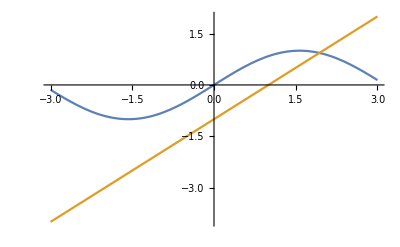

```mathematica
Plot[{Sin[x], x-1},{x, -3, 3}]
```

```mathematica
FindRoot[Sin[x]==x-1, {x, 2}] (* this uses Newton's method *)
```

{x→1.93456}

```mathematica
FindRoot[Sin[x]==x-1, {x, 1.5, 2.5}] (* this uses the secant method *)
```

{x→1.93456}

## Calculus

We’ve seen quite a bit of calculus already. Let’s recall.

```mathematica
D[x^3, x]
```

3 x^2

```mathematica
D[x^3, x,x]
```

6 x

```mathematica
D[x^3, x, x, x]
```

6

```mathematica
D[x Cos[y^2], x]
```

Cos[y^2]

```mathematica
D[x Cos[y^2], y]
```

-2 x y Sin[y^2]

```mathematica
D[x Cos[y^2], y,x]==D[x Cos[y^2], x,y](* what is this theorem? *)
```

True

```mathematica
Clear[f]
```

```mathematica
Integrate[f[x,y],{y, c, d}, {x, a, b} ]
```

∫_c^d ∫_a^b f[x,y]ⅆxⅆy

#### Problem 14.6

Consider . Generate the graph of  over the rectangle , . Find the maximum of  in this area.

Optimization problems are hard. The graph is easy though!

```mathematica
f[x_,y_]:=Sin[x+y] Cos[x^2 -y] - Sin[y]
s = D[f[x,y], x, y]
```

Cos[x+y] Sin[x^2-y]-2 x Cos[x+y] Sin[x^2-y]-Cos[x^2-y] Sin[x+y]+2 x Cos[x^2-y] Sin[x+y]

```mathematica
Plot3D[s, {x, -Pi, Pi}, {y, -Pi, Pi}]
```

-Graphics3D-

You should not expect in general to get algebraic solutions to optimizations. So we’ll use NMaximize (which is much faster than Maximize).

```mathematica
NMaximize[{s, -Pi <= x <= Pi, -Pi <= y <= Pi},{x,y}]
```

{7.28319,{x→-3.14159,y→2.57861}}

Bonus: plot the maximum on the surface.

```mathematica
s/.{x->-3.14,y-> 2.57}
```

7.27989